Settings

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

Lengths

Unit conversion
1. From hat quantities to km: requires calculation of ω_m 
2. From km to hat quantities

How is thetam related omegam?
ω_m=ω_v √((λ/ω_v-cos^2(2 θ_v))^2+sin^2(2 θ_v)) 
=> ω_m/ω_v=√(((sin 2 θ_v)/(tan 2 θ_m))^2+sin^2(2 θ_v))
and we know that 1 unit of ω_v is usally 10km scale (SHOULD DO A CALCULATION HERE)

```mathematica
ThetaMatter[thetav_,lambda_,omegav_:1]:=ArcTan[Sin[2thetav]/(Cos[2thetav]-lambda/omegav)]/2;
```

```mathematica
OmegaMatter[thetam_,thetav_,omegav_:1]:=omegav*Sqrt[Sin[thetav]^2+(Sin[2thetav]/Tan[2thetam])^2];
```

```mathematica
OmegaMatter2[lambda_,thetav_,omegav_:1]:=omegav*Sqrt[(lambda/omegav-Cos[2thetav])^2+Sin[2thetav]^2];
```

```mathematica
OmegaVacuum[energy_,deltam2_]:=deltam2/(2energy);(*input should be using the same units*)
```

```mathematica
MeVInverse2km[mev_]:=1.97*10^(-13)*(mev);(*  mev/1MeV=mev*(1/1MeV)=mev*(197fm)=...   *)
```

```mathematica
MeVInverse2km[1]
```

1.97×10^-13

Parameters

Vacuum parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
OmegaVacuum[energy10,deltamsquare13];
```

```mathematica
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2];
```

As a reference, MSW resonance density is (for 10 MeV neutrinos)

```mathematica
mswDensity10=(deltamsquare13*Cos[2thetaV]/(2 √2 gF energy10))*1.3*10^(41)*10^(-9)*1.67*10^(-24)/ye (*g/cc*)
```

3252.77

```mathematica
fraction=20
lambdaN=fraction*Cos[2thetaV]omegaV
```

20

2.4791×10^-15

```mathematica
thetamN=ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2;(*Pi/6*)
phiN=0;
kN=0.9999;
aN=0.1*lambdaN/OmegaMatter[thetamN,thetaV,omegaV](*(kN)^(-5/3)*);
endpointN=100000;
init={psi1[0],psi2[0]}=={1,0};
(*background potential BEGIN*)
kN0=0;
aN0=0;
(*background potential END*)
```

```mathematica
aN
```

0.00525762

Test the omega functions

```mathematica
OmegaMatter[thetamN,thetaV,omegaV]
OmegaMatter[thetamN,thetaV]
```

4.71525×10^-14

362.711

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/2 ahat Sin[2thetam](2n0)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = ( Abs[fun[khat,ahat,thetam,n0]]^2)/( Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/((-1+khat n0)^2+Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2)

```mathematica
amplitude[kN,aN,thetamN,1]
```

0.000476928

```mathematica
amplitude[0.00001,aN0,thetamN,1]
```

0.

```mathematica
(*resonanceWidthVSBackgroundDensityTicks=Table[{frac*Cos[2thetaV]omegaV,ScientificForm[mswDensity10*frac,2]},{frac,0.1,10}]*)
resonanceWidthVSBackgroundDensityTicks=Table[{frac,ScientificForm[mswDensity10*frac,2]},{frac,0.1,10}]
```

{{0.1,3.3×10^2},{1.1,3.6×10^3},{2.1,6.8×10^3},{3.1,1.×10^4},{4.1,1.3×10^4},{5.1,1.7×10^4},{6.1,2.×10^4},{7.1,2.3×10^4},{8.1,2.6×10^4},{9.1,3.×10^4}}

```mathematica
(*LogPlot[{Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda/omegaV)^2)]/2,1],Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda/omegaV)^2)]/2,2]},{lambda,0.1Cos[2thetaV]omegaV,10Cos[2thetaV]omegaV},PlotRange->Full,ImageSize->imgsize*1.2,Frame->True,FrameLabel->{{"Width/ω_m",None},{"λ (MeV)","ρ (g/cm^3)"}},PlotLabel->"Resonance Width and Background Matter Density",FrameTicks->{{Automatic,Automatic},{Automatic,resonanceWidthVSBackgroundDensityTicks}},PlotLegends->Placed[{"n=1","n=2"},{Center,Above}],GridLines->{{{Cos[2thetaV]omegaV,Red}},Automatic},GridLinesStyle->Directive[LightGray, Dashed],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]*)
LogPlot[{Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(frac*Cos[2thetaV])^2)]/2,1],Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(frac*Cos[2thetaV])^2)]/2,2]},{frac,0.1,10},PlotRange->Full,ImageSize->imgsize*1.2,Frame->True,FrameLabel->{{"Width/ω_m",None},{"λ/λ_msw","ρ (g/cm^3)"}},PlotLabel->"Resonance Width and Background Matter Density",FrameTicks->{{Automatic,Automatic},{Automatic,resonanceWidthVSBackgroundDensityTicks}},PlotLegends->Placed[{"n=1","n=2"},{Center,Above}],GridLines->{{{1,Red}},Automatic},GridLinesStyle->Directive[LightGray, Dashed],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
qFreq[k_,a_,thetam_,n_]:=Sqrt[fun[k,a,thetam,n]^2+(n k - 1)^2]
```

```mathematica
qFreqTicksFullk=Table[{k,ScientificForm[MeVInverse2km[1/(k*OmegaMatter[thetamN,thetaV,omegaV])],2]},{k,1,5}]
```

{{1,4.2},{2,2.1},{3,1.4},{4,1.},{5,8.4×10^-1}}

```mathematica
qFreqTicksFullq=Table[{q,ScientificForm[MeVInverse2km[1/(q*OmegaMatter[thetamN,thetaV,omegaV])],2]},{q,qFreq[1,aN,thetamN,1],qFreq[5,aN,thetamN,1],0.5}]
```

{{2.18439×10^-6,1.9×10^6},{0.500002,8.4},{1.,4.2},{1.5,2.8},{2.,2.1},{2.5,1.7},{3.,1.4},{3.5,1.2}}

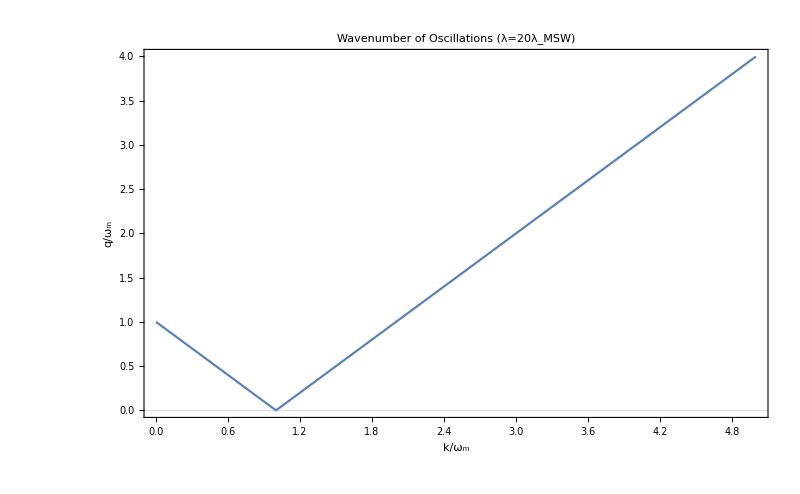

```mathematica
Plot[qFreq[k,aN,thetamN,1],{k,0,5},Frame->True,ImageSize->imgsize,PlotLabel->"Wavenumber of Oscillations (λ="<>ToString[fraction]<>"λ_MSW)",FrameLabel->{{"q/ω_m","Oscillation Wavelength (km)"},{"k/ω_m","Perturbation Wavelength (km)"}},FrameTicks->{{Automatic,qFreqTicksFullq},{Automatic,qFreqTicksFullk}},GridLines->{None,{qFreq[1,aN,thetamN,1]}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

```mathematica
probApprox[x_,nN_]:=amplitude[kN,aN,thetamN,nN](Sin[Sqrt[ Abs[fun[kN,aN,thetamN,nN]]^2+(nN kN - 1)^2]x/2])^2;
```

```mathematica
pltProbApprox=Plot[probApprox[x,1],{x,0,endpointN},PlotStyle->Blue,Frame->True,ImageSize->imgsize,PlotLabel->"Stimulated Oscillations with Approximation",PlotLegends->Placed[{Style["Approximation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
hN[x_]:=(aN Sin[kN x+phiN])Sin[2thetamN]Exp[I(-x-Cos[2thetamN] aN/kN Cos[kN x+phiN])]/2;
```

```mathematica
solN=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hN[x]},{Conjugate[hN[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointN},MaxSteps->10^6];

pltN=Plot[Evaluate[Abs[psi2[x]]^2/.solN],{x,0,endpointN},ImageSize->imgsize,Frame->True,FrameLabel->{"x̂","Transition Probability"},PlotStyle->{Red,Thickness[0.005],Dashing[{0.004,0.03}]},PlotLabel->"Stimulated Oscillations",PlotLegends->Placed[{Style["Numerical Calculation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
Show[pltProbApprox,pltN,FrameLabel->{"x̂","Transition Probability"},PlotLabel->"Stimulated Oscillations",LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

Remake Graph Using km

```mathematica
OmegaMatter[thetamN,thetaV,omegaV]
```

4.71525×10^-14

```mathematica
pltProbApproxTicksFull=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamN,thetaV,omegaV]],2]},{x,0,endpointN}];
```

```mathematica
pltProbApproxTicks=Take[pltProbApproxTicksFull,{1,Length@pltProbApproxTicksFull,Floor[(Length@pltProbApproxTicksFull)/5]}];
```

```mathematica
pltProbApproxTicks
```

{{0,0.},{20000,8.4×10^4},{40000,1.7×10^5},{60000,2.5×10^5},{80000,3.3×10^5},{100000,4.2×10^5}}

```mathematica
pltProbApprox2=Plot[probApprox[x,1],{x,0,endpointN},PlotStyle->Blue,Frame->True,ImageSize->imgsize,PlotLabel->"Stimulated Oscillations with Approximation",PlotLegends->Placed[{Style["Approximation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},FrameTicks->{{Automatic,None},{Automatic,pltProbApproxTicks}},FrameLabel->{{"Probability",None},{"x̂","Distance (km)"}}]
```

-Graphics-

```mathematica
Show[pltProbApprox2,pltN,PlotLabel->"Stimulated Oscillations (λ="<>ToString[fraction]<>"λ_MSw)"]
```

-Graphics-

The oscillation length of the matter profile

```mathematica
MeVInverse2km[kN/OmegaMatter[thetamN,thetaV,omegaV]](*km*)
```

4.17752

```mathematica
omegaV(√((OmegaMatter[thetamN,thetaV,omegaV]/omegaV)^2+Sin[2thetaV]^2)+Cos[2thetaV]^2)
```

4.72707×10^-14

Matter profile used here is

```mathematica
endpointNMatterProfile=Floor@endpointN/10
```

10000

```mathematica
frameTicksMatterProfile=Take[Table[{x,MeVInverse2km[x/OmegaMatter[thetamN,thetaV,omegaV]]},{x,0,endpointNMatterProfile}],{1,endpointNMatterProfile,Floor[(endpointNMatterProfile)/10]}]
```

{{0,0.},{1000,4177.93},{2000,8355.87},{3000,12533.8},{4000,16711.7},{5000,20889.7},{6000,25067.6},{7000,29245.5},{8000,33423.5},{9000,37601.4}}

```mathematica
(*Plot[aN(**OmegaMatter[thetamN,thetaV,omegaV]*)*Sin[kN*x],{x,0,endpointNMatterProfile},PlotPoints->Floor@endpointN,ImageSize->imgsize,Frame->True,FrameTicks->{{Automatic,None},{Automatic,frameTicksMatterProfile}},FrameLabel->{{"Perturbation Amplitude",None},{"x̂","Distance (km)"}},PlotLabel->"Matter Profile"]*)
```

Some Numbers

I would like to see what the corresponding matter perturbation wavelength for first resonance.
k=ω_m

For λ=0.1 ω_v, the condition is
k=ω_v √((0.1-Cos[2 θ_v])^2+Sin[2 θ_v]^2)

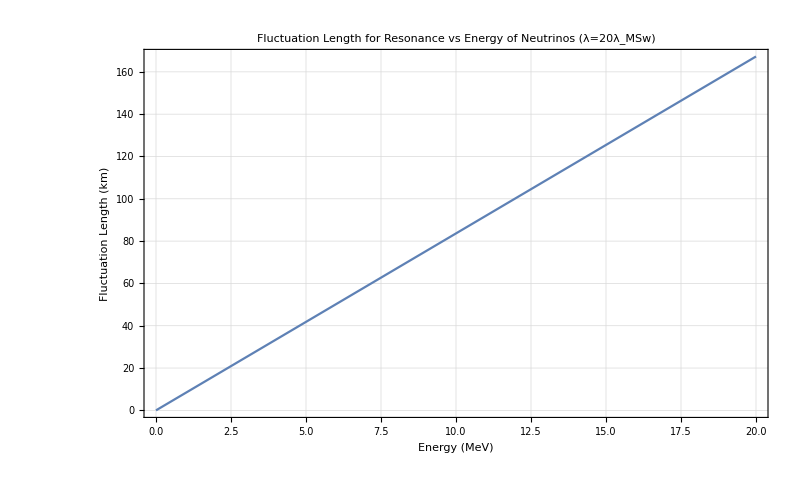

```mathematica
Plot[MeVInverse2km[1/OmegaMatter2[fraction*Cos[2thetaV]OmegaVacuum[ene,deltamsquare13],thetaV,OmegaVacuum[ene,deltamsquare13]]],{ene,0,20},Frame->True,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImageSize->imgsize,PlotLabel->"Fluctuation Length for Resonance vs Energy of Neutrinos (λ="<>ToString[fraction]<>"λ_MSw)",FrameLabel->{"Energy (MeV)","Fluctuation Length (km)"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Thin, Dashed]]
```